```mathematica
<<SpinWeightedSpheroidalHarmonics`
<<KerrGeodesics`
```

```mathematica
Source[l_,m_,k_,M_,a_,r0_,xi_]:=Module[
{ly=l,my=m,ky=k,My=M,ay=a,r0y=r0,xiy=xi,Δ,ℰ,ℒ,𝒬,Ωθ,Ωϕ,ω,Υ,Λ,Consts,Freqs,dtdλ,tp,rp,θp,ϕp,gtt,gtϕ,ut,orbit,Integrand,Ans},
Δ=r0y^2-2My r0y + ay^2;
Consts = KerrGeoConstantsOfMotion[ay,r0y,0,xiy];
ℰ=Consts[[1]];
ℒ=Consts[[2]];
𝒬=Consts[[3]];
Freqs= KerrGeoFrequencies[ay,r0y,0,xiy];
Ωθ = Freqs[[2]];
Ωϕ = Freqs[[3]];
ω = my Ωϕ + ky Ωθ;
Υ = KerrGeoFrequencies[ay,r0y,0,xiy,Time->"Mino"][[2]];
Λ=(2π)/Υ;
dtdλ = ℰ(((r0y^2+ay^2)^2)/Δ-ay^2 Sin[θp[λ]]^2)+ay ℒ(1-(r0y^2+ay^2)/Δ);
gtt = -((ay^4+2 r0y^4+ay^2 r0y (2 My+3 r0y)+ay^2 (ay^2+r0y (-2 My+r0y)) Cos[2 θp[λ]])/((ay^2+r0y (-2 My+r0y)) (ay^2+2 r0y^2+ay^2 Cos[2 θp[λ]])));
gtϕ=-(4 ay My r0y)/((ay^2+r0y (-2 My+r0y)) (ay^2+2 r0y^2+ay^2 Cos[2 θp[λ]]));
ut = gtϕ ℒ- gtt ℰ;
Integrand=SpinWeightedSpheroidalHarmonicS[0,ly,my,ay ω,θp[λ],0]/ut Cos[(ω tp[λ]-my ϕp[λ])]dtdλ;
orbit = KerrGeoOrbit[ay,r0y,0,xiy];
{tp,rp,θp,ϕp}=orbit["Trajectory"];

Ans=-(2Ωθ r0y)/Δ NIntegrate[Integrand,{λ,0,Λ},Method->"Trapezoidal"];
Ans
]
```

```mathematica
Initψout[l_,m_,kout_,a_,M_,ωi_] := 
Module[{i = l, j= m , N=kout, s = a, Μ=M, f0,f1,f2,f3,f4,f5,f6,n,ω=ωi,λ},
λ =SpinWeightedSpheroidalEigenvalue[0,i,j,s ω]-(s ω)^2+2 j s ω;

f0= -2 ⅈ n ω;
f1=n^2-λ+ω (-4 ⅈ Μ+s^2 ω)+n (-1+4 ⅈ Μ ω);
f2=-2 ⅈ s^2 (-2+n) ω+2Μ (-3+5 n-2 n^2+λ-2 s j ω+s^2 ω^2);
f3=4 Μ^2 (-2+n)^2+s^2 (8+j^2-8 n+2 n^2-λ);
f4=-2 a^2 Μ (15-11 n+2 n^2);
f5=s^4 (12-7 n+n^2);

cs = RecurrenceTable[{f0 c[n]+f1 c[n-1]+f2 c[n-2]+f3 c[n-3]+f4 c[n-4]+f5 c[n-5]==0,c[0]==1,c[-1]==0,c[-2]==0,c[-3]==0,c[-4]==0},c,{n,0,N}]
]
ψout[l_,m_,kout_,a_,M_,ω_,r_,c_]:=Exp[ⅈ ω (r+M Log[(r^2-2 M r +a^2)/M^2]+(2 M^2-a^2)/(2 √(M^2-a^2))Log[(r-M-√(M^2-a^2))/(r-M+√(M^2-a^2))])]Sum[c[[n+1]] r^-n,{n,0,kout}]
```

```mathematica
Initψin[l_,m_,kin_,a_,M_,ωi_] := 
Module[{i = l, j= m , N=kin, s = a, Μ=M,f,k,ω=ωi,γ,rp,λ},
rp= Μ+√(Μ^2-s^2);
γ = (2Μ rp ω-s j)/rp^2;
λ = SpinWeightedSpheroidalEigenvalue[0,i,j,s ω]-(s ω)^2+2 j s ω;
f= {s^4 (2-3 k+k^2)-4 s j Μ rp^3 ω+s^2 rp (rp (2+12 k^2+j^2+k (-18-8 ⅈ rp γ)-λ+rp^2 ω^2)+Μ (-6+24 k-12 k^2+2 rp^2 ω^2))+rp^2 (4 (1-9 k+6 k^2) Μ^2+2 Μ rp (-1-20 k^2+2 k (12+5 ⅈ rp γ)+λ)-rp^2 (-15 k^2+3 k (5+4 ⅈ rp γ)+λ+rp^2 (γ^2-ω^2))),2 (-6 s j Μ rp^2 ω+s^2 (rp (13+4 k^2+j^2+6 ⅈ rp γ+k (-15-6 ⅈ rp γ)-λ+2 rp^2 ω^2)+Μ (-10+9 k-2 k^2+3 rp^2 ω^2))+rp ((26-30 k+8 k^2) Μ^2+Μ rp (-49-20 k^2-20 ⅈ rp γ+k (66+20 ⅈ rp γ)+3 λ)+rp^2 (20+10 k^2+15 ⅈ rp γ+k (-30-15 ⅈ rp γ)-2 λ-3 rp^2 (γ^2-ω^2)))),4 (-3+k)^2 Μ^2+2 Μ rp (-71-10 k^2-40 ⅈ rp γ+k (54+20 ⅈ rp γ)+3 λ)-12 s j Μ rp ω+s^2 (18+2 k^2+j^2+16 ⅈ rp γ+k (-12-8 ⅈ rp γ)-λ+6 Μ rp ω^2+6 rp^2 ω^2)+rp^2 (90+15 k^2+80 ⅈ rp γ+k (-75-40 ⅈ rp γ)-6 λ-15 rp^2 (γ^2-ω^2)),2 (-ⅈ s^2 (-3+k) γ-15 ⅈ (-3+k) rp^2 γ-10 rp^3 (γ^2-ω^2)+Μ (-28-2 k^2-30 ⅈ rp γ+5 k (3+2 ⅈ rp γ)+λ-2 s j ω+s^2 ω^2)+rp (36-21 k+3 k^2-2 λ+2 s^2 ω^2)),4+(-4+k)^2-k+4 ⅈ (-4+k) Μ γ-12 ⅈ (-4+k) rp γ-λ+s^2 ω^2-15 rp^2 (γ^2-ω^2),-2 ⅈ (-5+k) γ-6 rp γ^2+6 rp ω^2,-γ^2+ω^2};

cs = RecurrenceTable[{c[k] f⟦1⟧+c[-1+k] f⟦2⟧+c[-2+k] f⟦3⟧+c[-3+k] f⟦4⟧+c[-4+k] f⟦5⟧+c[-5+k] f⟦6⟧+c[-6+k] f⟦7⟧==0,c[0]==1,c[-1]==0,c[-2]==0,c[-3]==0,c[-4]==0,c[-5]==0},c,{k,0,N}]
]
ψin[l_,m_,kin_,a_,M_,ω_,r_,c_]:=Exp[-ⅈ ((2M(M+√(M^2-a^2))ω-a m)/((M+√(M^2-a^2))^2)) (r+M Log[(r^2-2 M r +a^2)/M^2]+(2 M^2-a^2)/(2 √(M^2-a^2))Log[(r-M-√(M^2-a^2))/(r-M+√(M^2-a^2))])]Sum[c[[n+1]](r-M-√(M^2-a^2))^n,{n,0,kin}]
```

```mathematica
rs[r_]:=r+M Log[((r-M-√(M^2-a^2))(r-M+√(M^2-a^2)))/M^2] +(2 M^2-a^2)/(2 √(M^2-a^2)) Log[(r-M-√(M^2-a^2))/(r-M+√(M^2-a^2))];
```

```mathematica
l=3;
m=1;
k=2;

M=1`32;
a=.998`32M;
rp =M+√(M^2-a^2);
rout=(1`32)10^5 M;
rin = (1`32)10^-5 M+rp;

r0=10`32M;
x = Cos[π/3`32];

kout=100;
kin=100;

Freqs = KerrGeoFrequencies[a,r0,0,x];
Ωθ = Freqs[[2]];
Ωϕ = Freqs[[3]];

ω = m Ωϕ + k Ωθ;
γ =a ω;
λ = SpinWeightedSpheroidalEigenvalue[0,l,m,a ω]-γ^2+2m γ;

Δ[r_]:=r^2-2M r+a^2;
W[r_]:=(((r^2+a^2)ω-a m)/r^2)^2-Δ[r]/r^4(λ-2 a m ω +a^2 ω^2+(2(M r-a^2))/r^2)

Outcs = Initψout[l,m,kout,a,M,ω];
Incs = Initψin[l,m,kin,a,M,ω];

OuterBoundary=ψout[l,m,kout,a,M,ω,rout,Outcs];
InnerBoundary=ψin[l,m,kin,a,M,ω,rin,Incs];


OuterDeriv = D[ψout[l,m,kout,a,M,ω,r,Outcs],r]/.{r->rout};
InnerDeriv = D[ψin[l,m,kin,a,M,ω,r,Incs],r]/.{r->rin};
```

```mathematica
Nψin=ψ/.NDSolve[{Δ[r]^2/r^4 ψ''[r]+(2Δ[r](r^2(r-M)-Δ[r]r))/r^6 ψ'[r]+W[r]ψ[r]==0,ψ'[rin]==InnerDeriv,ψ[rin]==InnerBoundary},ψ,{r,rin,r0}][[1]];
Nψout=ψ/.NDSolve[{Δ[r]^2/r^4 ψ''[r]+(2Δ[r](r^2(r-M)-Δ[r]r))/r^6 ψ'[r]+W[r]ψ[r]==0,ψ'[rout]==OuterDeriv,ψ[rout]==OuterBoundary},ψ,{r,rout,r0}][[1]];
```

```mathematica
α = Source[l,m,k,M,a,r0,x];
cHor = α Nψout[r0]/(Nψin[r0]Nψout'[r0]-Nψout[r0]Nψin'[r0]);
```

```mathematica
cInf = cHor Nψin[r0]/Nψout[r0];
```

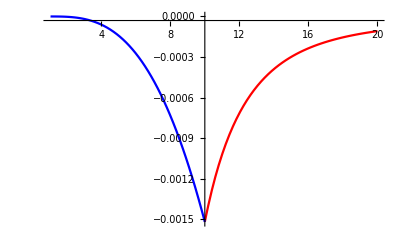

```mathematica
Show[Plot[{Re[cInf Nψout[r]/r]},{r,r0,20},PlotStyle->{Red},PlotRange->All],
Plot[{Re[cHor Nψin[r]/r]},{r,rin,r0},PlotStyle->{Blue}],
PlotRange->All]
```

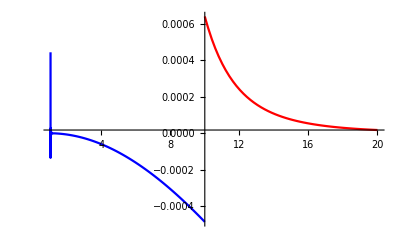

```mathematica
Show[Plot[{Re[cInf D[ Nψout[r]/r,r]/.{r->ρ}]},{ρ,r0,20},PlotStyle->{Red},PlotRange->All],
Plot[{Re[cHor D[Nψin[r]/r,r]/.{r->ρ}]},{ρ,rin,r0},PlotStyle->{Blue}],
PlotRange->All]
```

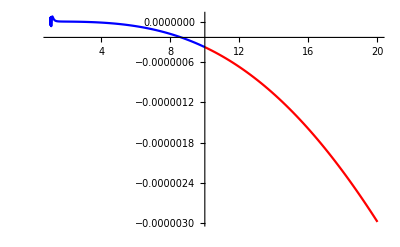

```mathematica
Show[
Plot[{Im[cInf Nψout[r]/r]},{r,r0,20},PlotStyle->{Red},PlotRange->All],
Plot[{Im[cHor Nψin[r]/r]},{r,rin,r0},PlotStyle->{Blue}],
PlotRange->All]
```

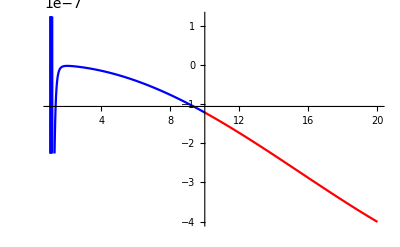

```mathematica
Show[
Plot[{Im[cInf D[Nψout[r]/r,r]/.{r->ρ}]},{ρ,r0,20},PlotStyle->{Red},PlotRange->All],
Plot[{Im[cHor D[Nψin[r]/r,r]/.{r->ρ}]},{ρ,rin,r0},PlotStyle->{Blue}],
PlotRange->All]
```